```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/phi3/2loop

```mathematica
<<LiteRed2`
(*<<Mint`*)
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 22:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
(*GetEnvironment["PATH"][[2]]
SetEnvironment["PATH"->GetEnvironment["PATH"][[2]]<>":/usr/local/bin"]
<<PolyLogTools`
$HPLAutoConvertToKnownFunctions = True*)
```

```mathematica
convert=Table[ToExpression["topo"<>ToString[i]]-> ToExpression["IF"<>ToString[i]], {i,1,2}];
intfamvoc=Table[ToExpression["IF"<>ToString[i]],{i,1,2}];
```

## Integral family definition topo1

### Preliminaries

```mathematica
family = topo1;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {sp[k1,k1]-m2, sp[k2,k2]-m2, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m2,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m2,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m2}
props ={ "props"->{k1,k2,k1+k2, k1-p,k2+p  }, "every prop is massive with mass^2 "->{m2}, "invariant is p^2 = pp"}
Export["./definitions/props.m",props]
MI={j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]} /. j[topo1,a__] -> topo1[a];
Export["./definitions/masters.m", MI]
```

{-m2+k1·k1,-m2+k2·k2,-m2+k1·k1+2 k1·k2+k2·k2,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2+2 k2·p}

{props→{k1,k2,k1+k2,k1-p,k2+p},every prop is massive with mass^2 →{m2},invariant is p^2 = pp}

./definitions/props.m

./definitions/masters.m

```mathematica
(*(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2},Directory->"topo1"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];

(*Save to disk*)
DiskSave[family];*)
```

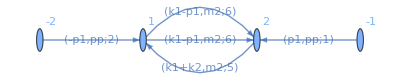

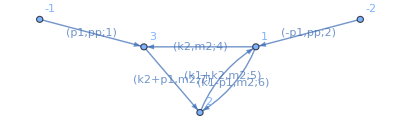

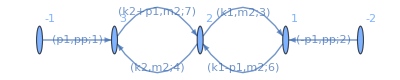

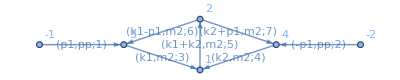

```mathematica
(*Import["./graphs/topo1/all/topo1_2_24.dot"]
Import["./graphs/topo1/all/topo1_3_28.dot"]
Import["./graphs/topo1/all/topo1_3_26.dot"]*)
Import["./graphs/topo1/all/topo1_3_14.dot"]
Import["./graphs/topo1/all/topo1_4_30.dot"]
Import["./graphs/topo1/all/topo1_4_27.dot"]
Import["./graphs/topo1/all/topo1_5_31.dot"]
```

```mathematica
Get["./topo1/topo1"];
```

```mathematica
MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];
(*Put[mis,"./Reduction/FamRed/"<>ToString[family]<>"/"<>"Mi"]
MIs[family];*)
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
(*LiteRed Masters*)
todiff= MIs[family];
```

```mathematica
(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;
```

```mathematica
startBasis=Import["./rot/startBasis.m"] /. topo1[a__]-> j[topo1,a];
```

```mathematica
T=CoefficientArrays[(IBPReduce[startBasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ startBasis]//Together//Union;
invT = (Inverse[T]//Simplify);
Mpp=(D[T,pp].invT//Simplify) + T.MppLiteRed.(invT)//Simplify;
Mm2=(D[T,m2].invT//Simplify) + T.Mm2LiteRed.(invT)//Simplify;
Mpp=Mpp /. m2 -> 1 /. pp -> ρ /. d-> 4 -2 eps ;
Mm2=Mm2 /. m2 -> 1 /. pp -> ρ /. d-> 4 -2 eps ;
```

```mathematica
combineOperator = { F1[a__]F2[b__] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b] };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
{sol[0][0], sol[0][1], coeff}=Import["./PERIODS/omega0.m"]/.extractPolySol;
d2omega0 = Import["./PERIODS/d2omega0.m"];
T1 = Import["./rot/T1.m"];
T1Inv= Inverse[T1]// Simplify;
T1derInv=D[ T1Inv /. ω0 -> ω0[ρ] /.dω0 -> D[ω0[ρ],ρ],ρ] /. ω0[ρ] ->ω0 /. ω0'[ρ]-> dω0/. ω0''[ρ]-> d2ω0 /.d2omega0  //Simplify;
EPS = Import["./rot/EPS.m"]
T2 = Import["./rot/T2.m"];
T2Inv= Inverse[T2]// Simplify;
T2derInv=D[ T2Inv  /. ω0 -> ω0[ρ],ρ]  /.d2omega0 /. ω0[ρ] ->ω0 /. ω0'[ρ]-> dω0 //Simplify;
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,eps,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Mpp
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-(2 eps)/(√(4-ρ) √ρ),0,(2 eps)/(8-2 ρ),0,0,0,0,0},{0,0,0,0,1,0,0,0},{(6 eps^2)/((1-ρ) (9-ρ) ρ),0,0,-((-1-2 eps) (6-2 eps+(-2-2 eps) ρ))/(2 (1-ρ) (9-ρ) ρ),(-9 (2-2 eps)-10 (-4-2 eps) ρ+3 (-2-2 eps) ρ^2)/(2 (1-ρ) (9-ρ) ρ),0,0,0},{0,-eps/(√((4-ρ) ρ)),0,(-4-2 eps)/(6 √((4-ρ) ρ)),-(5 ρ)/(3 √((4-ρ) ρ)),(2 eps)/(8-2 ρ),0,0},{0,0,(4 eps)/(√(4-ρ) √ρ),0,0,0,(2 eps)/(4-ρ),0},{0,0,0,-(2 eps (6-ρ))/(72-24 ρ),0,-(3 eps)/(4 (3-ρ) √((4-ρ) ρ)),-(2 eps)/(96-32 ρ),-eps/(-3+ρ)}}

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[2]=Inverse[EPS].newMpp[1].EPS   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
newMpp[3]=(T2derInv.T2//Simplify)+T2Inv.newMpp[2].T2   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
```

```mathematica
tocheck=newMpp[3];
```

```mathematica
newMpp[3]/. eps -> 0//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(10 dω0 ρ (9-10 ρ+ρ^2)+4 (9-10 ρ+ρ^2) ω0)/(6 (-9+ρ) (-1+ρ) √(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*EllipticPi[ ... ] *)
```

```mathematica
(*4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2)))*)
```

```mathematica
g4derdef = Import["./rot/g4def.m"];
```

```mathematica
R = Import["./rot/R.m"];
Rinv = Inverse[R]// Simplify
derRinv=(D[Rinv, ρ] // Simplify)/. ω0[ρ] ->ω0 /. ω0'[ρ]-> dω0/. ω0''[ρ]-> d2ω0 /.d2omega0  /. g4derdef// Simplify;
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,-g4[ρ]+(5 ρ ω0[ρ])/(3 √(-((-4+ρ) ρ))),0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
newMpp[4]=(derRinv.R//Simplify)+Rinv.newMpp[3].R  /.ω0[ρ]-> ω0/. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
```

```mathematica
newMpp[4] //Simplify //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (eps (-8 √(-((-4+ρ) ρ)) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | 0 | 0 | -(eps (ρ (9-10 ρ+ρ^2) ω0+9 √(-((-4+ρ) ρ)) g4[ρ]))/(12 (-4+ρ) (-3+ρ) ρ) | 0 | (3 eps)/(4 (-3+ρ) √(-((-4+ρ) ρ))) | eps/(16 (-3+ρ)) | -eps/(-3+ρ))

```mathematica
Export["./rot/epsilon_factorised.m",newMpp[4]]
```

./rot/epsilon_factorised.m

```mathematica
adjustconventions={ √(-((-4+ρ) ρ)) -> Sqrt[(4-ρ)]Sqrt[ρ], 1/√(-((-4+ρ) ρ)) -> 1/ Sqrt[(4-ρ)]/Sqrt[ρ], 1/(ρ-4) -> -1/(4-ρ)}
LogForms = {(9+10 ρ-3 ρ^2)/(2 (-9+ρ) (-1+ρ) ρ),1/(-3+ρ) /√(4-ρ)/Sqrt[ρ],1/(4-ρ),1/√(4-ρ)/Sqrt[ρ],1/(-3+ρ)}/.adjustconventions;
Ellforms =  { g4[ρ]/((-9+ρ) (-1+ρ) ρ ω0^2) ,((3+ρ)^4 ω0^2)/((-9+ρ) (-1+ρ) ρ) ,(-8 √(4-ρ)Sqrt[ρ] (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ])/((-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)   , 1/((-9+ρ) (-1+ρ) ρ ω0^2),(ρ (9-10 ρ+ρ^2) ω0+9 √(4-ρ)Sqrt[ρ] g4[ρ])/((4-ρ) (-3+ρ) ρ), ω0 }/.adjustconventions;
nameLogForm = Thread[Rule[LogForms, Table[l[i],{i,1,Length[LogForms]}]]]
nameEllForm = Thread[Rule[Ellforms, Table[EF[i],{i,1,Length[Ellforms]}]]]
```

{√(-((-4+ρ) ρ))→√(4-ρ) √ρ,1/(√(-((-4+ρ) ρ)))→1/(√(4-ρ) √ρ),1/(-4+ρ)→-1/(4-ρ)}

{(9+10 ρ-3 ρ^2)/(2 (-9+ρ) (-1+ρ) ρ)→l[1],1/(√(4-ρ) (-3+ρ) √ρ)→l[2],1/(4-ρ)→l[3],1/(√(4-ρ) √ρ)→l[4],1/(-3+ρ)→l[5]}

{g4[ρ]/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[1],((3+ρ)^4 ω0^2)/((-9+ρ) (-1+ρ) ρ)→EF[2],(-8 √(4-ρ) √ρ (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ])/((-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)→EF[3],1/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[4],(ρ (9-10 ρ+ρ^2) ω0+9 √(4-ρ) √ρ g4[ρ])/((4-ρ) (-3+ρ) ρ)→EF[5],ω0→EF[6]}

```mathematica
Export["./FORMS/log_forms.m", nameLogForm]
Export["./FORMS/ell_forms.m", nameEllForm]
```

./FORMS/log_forms.m

./FORMS/ell_forms.m

```mathematica
ser=Series[nameLogForm[[;;,1]], {ρ,0,40}]//Normal;
```

```mathematica
omega0Sol=ω0-> sol[0][0 ] /. extractPolySol;
g4Series=g4[ρ]-> Collect[Integrate[Series[g4derdef[[2]] /. omega0Sol, {ρ,0,39}]//Normal, ρ], {ρ}, Simplify] /. ρ^a_ /; a> 39 -> 0;
EllSeries=Series[nameEllForm[[;;,1]] /. omega0Sol /. g4Series, {ρ,0,39}]//Normal;
```

```mathematica
ExpansionMat=Collect[Series[newMpp[4] /. eps -> 1  /. g4Series/.nameEllForm /. nameLogForm /.Thread[Rule[nameLogForm[[;;,2]],ser]] /. Thread[Rule[nameEllForm[[;;,2]],EllSeries]], {ρ,0,39}]//Normal, {ρ},Simplify];
```

```mathematica
Series[ExpansionMat, {ρ,0,0}]//Normal
(Coefficient[%,ρ,-1].{i1,i2,i3,i4,i5,i6,i7,i8}//Union)[[2;;]]
(*i5 -> -1/2i4 *)
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-1/(√ρ),0,1/4,0,0,0,0,0},{0,0,0,10/9+1/(2 ρ),4/9+1/ρ,0,0,0},{2/3,0,0,7/9+1/(4 ρ),10/9+1/(2 ρ),0,0,0},{0,-1/(2 √ρ),0,-1/(4 √ρ),-1/(6 √ρ),1/4,0,0},{0,0,2/(√ρ),0,0,0,1/2,0},{0,0,0,-1/12,0,-1/(8 √ρ),-1/48,1/3}}

{i4/4+i5/2,i4/2+i5}

## Solutions

#### Boundary Condition

Explicit integrals

```mathematica
Tad[n_]:=E^(EulerGamma eps)(-1 )(m2)^((d-2n)/2)Gamma[n-d/2]/Gamma[n] 
(*Series[eps Tad[2] /. d ->4-2eps, {eps,0,3}]// FullSimplify*)
cantedExp =(Collect[Series[Tad[2] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,5}]//Normal, {eps}, FullSimplify]);
```

```mathematica
(*family = bub;
SetDim[d];
Declare[
{p,k1},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
intfam  = {sp[k1,k1]-m2,sp[k1,k1] + sp[p,p] + 2 sp[p,k1] -m2}
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1},Directory->"bub"]
GenerateIBP[family];
AnalyzeSectors[family];
FindSymmetries[family];
(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];
(*Save to disk*)
DiskSave[family];
laporta ={ j[bub,0,1], j[bub,1,1]};
canonB ={ eps j[bub,0,2],eps √(4-pp) √pp j[bub,2,1]};
der=(Dinv[canonB,pp]//IBPReduce) /. m2 -> 1 /. pp -> ρ;dermat=(CoefficientArrays[der, laporta][[2]]//Normal);
T=CoefficientArrays[IBPReduce[canonB]/.m2-> 1 /. pp -> ρ,laporta ][[2]]//Normal;
deq =(dermat.Inverse[T]/. d-> 4 -2 eps //Simplify)/. 1/√(-((-4+ρ) ρ)) -> 1/√(4-ρ)/Sqrt[ρ]/.eps :> 1;
deq  //MatrixForm*)
```

```mathematica
(*deq ={{0,0},{-1/(√(4-ρ) √ρ),1/(4-ρ)}};
(*
laporta =  Laporta2CanonBub . CanonB
*)
Laporta2CanonBub={{2/((-2+d) eps),0},{1/((-3+d) eps),(√(4-ρ))/((-3+d) eps √ρ)}}/.d-> 4-2eps//Simplify//Factor;
Canon2LaportaBub=Inverse[Laporta2CanonBub]//Simplify;
laporta={j[bub,0,1],j[bub,1,1]};
canonB={eps j[bub,0,2],eps √(4-ρ) √ρ j[bub,2,1]};
deqNamed=deq/. nameLogForm*)
```

```mathematica
(*The canonical bubble vanish in the limit of 0 momentum *)
(*const = {Collect[Series[eps Tad[2] /. m2-> 1/. d-> 4 -2 eps, {eps,0,6}]//Normal, {eps}, FullSimplify],0}*)
```

```mathematica
(*sol0 =Coefficient[const,eps,0]II[];
sol1 = (deqNamed.sol0 /. II[]l[a_] -> II[l[a]]) + Coefficient[const,eps,1];
sol2 = (Expand[deqNamed.sol1 ]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]}) + Coefficient[const,eps,2];
sol3 = (Expand[deqNamed.sol2] /. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]}) + Coefficient[const,eps,3];
sol4 = (Expand[deqNamed.sol3] /. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]}) + Coefficient[const,eps,4];
sol5 = (Expand[deqNamed.sol4 ]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]}) + Coefficient[const,eps,5];*)
```

```mathematica
(*FULLSOLbubTad = sol0 + eps sol1 + eps^2 sol2 + eps^3 sol3 +eps^4 sol4+eps^5 sol5;*)
```

```mathematica
(*Export["./solutions/bubtad/canon_basis.m", canonB];
Export["./solutions/bubtad/laporta.m", laporta];
Export["./solutions/bubtad/Laporta2CanonBub.m",Laporta2CanonBub];
Export["./solutions/bubtad/sol.m", FULLSOLbubTad];*)
```

Boundary conditions

```mathematica
amflow = Import["./amflow/amflow_solution.m"];
amflow=Thread[Rule[amflow[[;;,1]],Series[amflow[[;;,2]]Normal[Series[E^(2 EulerGamma eps), {eps,0,8}]], {eps,0,5}]//Normal]];
```

```mathematica
(*N[amflow[[1,2]],20]
Series[(Collect[Series[ Tad[1] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,8}]//Normal, {eps}, FullSimplify])^2, {eps,0,5}]//Normal//N
%%-%//Chop*)
```

```mathematica
basisCanon=Inverse[R].Inverse[T2].Inverse[EPS].Inverse[T1].startBasis/.d-> 4-2eps//Simplify;
```

```mathematica
(* boundary constants *)
(*
The first integral has a non trivial expansion 
2nd integral starts at O(eps^2) 
3nd integral is = 0 to all orders
4nd integral starts at O(eps^2)
5nd integral starts at O(eps^2)
6nd integral is  0 to all orders
7nd integral is  0 to all orders
8nd integral is  0 to all orders
*)
boundary[1]=Series[(basisCanon[[1]]//IBPReduce)/. m2-> 1 /. j[topo1,0,0,0,1,1]-> Tad[1]^2 /. m2-> 1 /. d-> 4 -2 eps, {eps,0,6}]//Normal//FullSimplify
boundary[2]=Series[(basisCanon[[2]]//IBPReduce) /. d -> 4 -2 eps /. m2 -> 1 /. amflow, {eps,0,4}]//Normal
boundary[3]=Series[(basisCanon[[3]]//IBPReduce) /. d -> 4 -2 eps /. m2 -> 1 /. amflow /. pp -> 0, {eps,0,4}]//Normal
boundary[4]=Series[(basisCanon[[4]] // IBPReduce)/. d -> 4 -2 eps /. m2 -> 1/. pp -> 0 /. amflow /. omega0Sol /. ρ -> 0, {eps,0,4}]//Normal
boundary[5]=Series[(basisCanon[[5]] // IBPReduce)/. d -> 4 -2 eps /. m2 -> 1/. pp -> 0 /. amflow /. omega0Sol /. ρ -> 0, {eps,0,4}]//Normal
boundary[6]=Series[Series[(Series[(basisCanon[[6]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
boundary[7]=Series[Series[(Series[(basisCanon[[7]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
boundary[8]=Series[Series[(Series[(basisCanon[[8]] // IBPReduce)/. d -> 4 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
```

4+(2 eps^2 π^2)/3+(7 eps^4 π^4)/90+(31 eps^6 π^6)/3780-4/9 eps^3 (6+eps^2 π^2) Zeta[3]+8/9 eps^6 Zeta[3]^2-8/5 eps^5 Zeta[5]

-9.375628954757835562406249155489108276381612038543425042665200755602643815819418617114434849986518332252508203078108429 eps^2+16.15030452706328802053930248293475300269471564328464438444235958883895845622280017956586493972990829418056296744823522 eps^3-47.592539527227664743904938898757931873066839650663242985388381413061148668650009497141538640969083510090096651611060902 eps^4

0

-9.375628954757835562406249155489108276381612038543425042665200755602643815819418617114434849986518332252508203078108429 eps^2+16.15030452706328802053930248293475300269471564328464438444235958883895845622280017956586493972990829418056296744823522 eps^3-47.5925395272276647439049388987579318730668396506632429853883814130611486686500094971415386409690835100900966516110609 eps^4

4.687814477378917781203124577744554138190806019271712521332600377801321907909709308557217424993259166126254101539054215 eps^2-8.075152263531644010269651241467376501347357821642322192221179794419479228111400089782932469864954147090281483724117612 eps^3+23.79626976361383237195246944937896593653341982533162149269419070653057433432500474857076932048454175504504832580553045 eps^4

√O[ρ]

0

0

```mathematica
{Log[2]^4,Log[3]^4,Log[2]^2 Log[3]^2,π Log[2]^3,π Log[3]^3,π Log[2]^2 Log[3],π Log[2] Log[3]^2,π^2 Log[2]^2,π^2 Log[3]^2,π^2 Log[2] Log[3],π^3 Log[2],π^3 Log[3],Log[2] Zeta[3],Log[3] Zeta[3],Log[2] Log[3]^3}/Sqrt[3]
```

{Log[2]^4/(√3),Log[3]^4/(√3),(Log[2]^2 Log[3]^2)/(√3),(π Log[2]^3)/(√3),(π Log[3]^3)/(√3),(π Log[2]^2 Log[3])/(√3),(π Log[2] Log[3]^2)/(√3),(π^2 Log[2]^2)/(√3),(π^2 Log[3]^2)/(√3),(π^2 Log[2] Log[3])/(√3),(π^3 Log[2])/(√3),(π^3 Log[3])/(√3),(Log[2] Zeta[3])/(√3),(Log[3] Zeta[3])/(√3),(Log[2] Log[3]^3)/(√3)}

```mathematica
w2const = { π^2,Im[PolyLog[2,E^(π/3 I)]]/Sqrt[3],Log[2] Log[3],Log[2]^2,Log[3]^2};
w3const = {Pi^3/√3, π Im[PolyLog[2,ⅇ^((ⅈ π)/3)]]/Sqrt[3],Im[PolyLog[3,ⅈ/(√3)]]/Sqrt[3],Im[PolyLog[3,1/2 ⅇ^((ⅈ π)/3)]]/Sqrt[3],π Log[2]^2,π Log[3]^2/Sqrt[3],π^2 Log[3],π^2 Log[2],Log[2]^3,Log[3]^3,Im[PolyLog[2,ⅇ^((ⅈ π)/3)]]Log[3]/Sqrt[3],Im[PolyLog[2,ⅇ^((ⅈ π)/3)]]Log[2]/Sqrt[3],Log[2] Log[3]^2,Log[2]^2 Log[3],Log[2] PolyLog[2,-1/2], PolyLog[3,-1/2],PolyLog[3,1/3],Zeta[3]} ;
w4const={(*Pure constants*)Pi^4,Pi Zeta[3],(*Clausen sector*)Cl[4,Pi/3],Cl[2,Pi/3]^2,Pi^2 Cl[2,Pi/3],Cl[2,Pi/3] PolyLog[2,-(1/2)],(*PolyLog weight 4*)PolyLog[4,-(1/2)],PolyLog[4,1/3],PolyLog[4,1/2],PolyLog[4,2/3],(*Imaginary parts—weight 4*)Im[PolyLog[4,-I/Sqrt[3]]],Im[PolyLog[4,1/2 Exp[I Pi/3]]],(*Im[H[0,1,1,-1,Exp[I Pi/3]]],*)(*Weight 3×Pi*)Pi Im[PolyLog[3,I/Sqrt[3]]],Pi Im[PolyLog[3,1/2 Exp[I Pi/3]]],(*Weight 3×logs*)Log[2] Im[PolyLog[3,I/Sqrt[3]]],Log[2] Im[PolyLog[3,1/2 Exp[I Pi/3]]],Log[3] Im[PolyLog[3,I/Sqrt[3]]],Log[3] Im[PolyLog[3,1/2 Exp[I Pi/3]]],(*Dilog products*)PolyLog[2,-(1/2)]^2,(*Log sector*)Log[2]^4,Log[3]^4,Log[2]^2 Log[3]^2,(*Pi–Log sector:π log^3*)Pi Log[2]^3,Pi Log[3]^3,Pi Log[2]^2 Log[3],Pi Log[2] Log[3]^2,(*Pi–Log sector:π^2 log^2*)Pi^2 Log[2]^2,Pi^2 Log[3]^2,Pi^2 Log[2] Log[3],(*Pi–Log sector:π^3 log*)Pi^3 Log[2],Pi^3 Log[3],(*Log–zeta*)Log[2] Zeta[3],Log[3] Zeta[3],Log[2] Log[3]^3,Cl[2,π/3] Log[2]^2, π^2 PolyLog[2,-1/2], Log[2] Log[3] PolyLog[2,-1/2],Log[2]^2 PolyLog[2,-1/2], Log[2] PolyLog[3,-1/2], Log[2] PolyLog[3,1/3], Log[3] PolyLog[3,1/3],Cl[2,π/3] Log[2] Log[3],π^4/Sqrt[3],(π Log[2]^3)/(√3),(π Log[3]^3)/(√3),(π Log[2]^2 Log[3])/(√3),(π Log[2] Log[3]^2)/(√3),(π^2 Log[2]^2)/(√3),(π^2 Log[3]^2)/(√3),(π^2 Log[2] Log[3])/(√3),(π^3 Log[2])/(√3), Im[PolyLog[3,ⅈ/(√3)]] Log[3]/Sqrt[3]} /. Cl[a_,ph_] :> Im[PolyLog[a, E^( I ph)]];
```

```mathematica
boundaryExact[2] = n[2,2]eps^2 + n[2,3]eps^3+n[2,4]eps^4;
boundaryExact[4] = n[4,2]eps^2 + n[4,3]eps^3+n[4,4]eps^4;
boundaryExact[5] = n[5,2]eps^2 + n[5,3]eps^3+n[5,4]eps^4;
```

```mathematica
FindIntegerNullVector[Join[{Coefficient[boundary[2],eps,2]}, w2const]].Join[{Coefficient[boundaryExact[2],eps,2]},w2const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[4],eps,2]}, w2const]].Join[{Coefficient[boundaryExact[4],eps,2]},w2const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[5],eps,2]}, w2const]].Join[{Coefficient[boundaryExact[5],eps,2]},w2const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[2],eps,3]}, w3const]].Join[{Coefficient[boundaryExact[2],eps,3]},w3const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[4],eps,3]}, w3const]].Join[{Coefficient[boundaryExact[4],eps,3]},w3const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[5],eps,3]}, w3const]].Join[{Coefficient[boundaryExact[5],eps,3]},w3const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[2],eps,4]}, w4const]].Join[{Coefficient[boundaryExact[2],eps,4]},w4const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[4],eps,4]}, w4const]].Join[{Coefficient[boundaryExact[4],eps,4]},w4const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[5],eps,4]}, w4const]].Join[{Coefficient[boundaryExact[5],eps,4]},w4const]==0 //Solve//Flatten;
solutionsFitPSLQ=Join[%,%%,%%%,%%%%,%%%%%,%%%%%%,%%%%%%%,%%%%%%%%,%%%%%%%%%];
```

```mathematica
const = {4+(2 eps^2 π^2)/3+(7 eps^4 π^4)/90+(31 eps^6 π^6)/3780-4/9 eps^3 (6+eps^2 π^2) Zeta[3]+8/9 eps^6 Zeta[3]^2-8/5 eps^5 Zeta[5], n[2,2]eps^2 + n[2,3]eps^3+ n[2,4]eps^4,0, n[4,2]eps^2 + n[4,3]eps^3+ n[4,4]eps^4, n[5,2]eps^2 + n[5,3]eps^3+n[5,4]eps^4,0,0,0}/. solutionsFitPSLQ;
```

#### formal solution

```mathematica
Deq = Import["./rot/epsilon_factorised.m"] /.adjustconventions;
DeqNamed = Deq /.nameEllForm  /. nameLogForm /. eps ->1;
```

```mathematica
c[0] =Coefficient[const,eps,0] II[];
c[1] = Coefficient[const,eps,1]II[];
c[2] = Coefficient[const,eps,2]II[];
c[3] = Coefficient[const,eps,3]II[];
c[4] = Coefficient[const,eps,4]II[];
tmp1 =Expand[ DeqNamed.c[0]]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]} ;
sol1  = tmp1 + c[1];
tmp1 =Expand[ DeqNamed.sol1]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol2  = tmp1 + c[2];
tmp1 =Expand[ DeqNamed.sol2]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol3  = tmp1 + c[3];
tmp1 =Expand[ DeqNamed.sol3]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol4  = tmp1 + c[4];
```

```mathematica
FULLSOL = c[0] +  eps sol1 +eps^2  sol2 + eps^3 sol3+ eps^4 sol4;
```

## Corr d ~ 4

```mathematica
CanBasisRed= Collect[IBPReduce[basisCanon]/.pp -> ρ /. m2 -> 1/.d-> 4-2eps, {_j },Simplify];
Union@Cases[CanBasisRed, _j, ∞];
laporta = MIs[topo1];
Complement[%%,%]
mat=CoefficientArrays[CanBasisRed,laporta][[2]]//Normal;
invmat=Inverse[mat]//Simplify;
```

{}

```mathematica
coupl = λ^2
```

λ^2

```mathematica
Amp=1/8*INT[topoA,1,1,0,0,0]*lmbda^4+1/2*INT[topoA,1,1,1,1,1]*lmbda^4+1/4*INT[topoA,1,1,2,0,0]*lmbda^4+1/4*INT[topoA,2,1,0,0,0]*lmbda^4+1/2*INT[topoA,2,1,0,1,0]*lmbda^4+1/2*INT[topoA,2,1,1,1,0]*lmbda^4 /. lmbda -> 1 /. INT[topoA,a__]-> j[topo1,a];
```

```mathematica
Amp = Collect[Amp  // IBPReduce, {_j}, Together]/.m2-> 1;
```

```mathematica
(* Amp = AmpRedCanon . CANON *)
AmpRedCanon=(CoefficientArrays[Amp /. m2 -> 1 /. pp -> ρ, laporta][[2]]//Normal).invmat /. d -> 4 -2 eps//Simplify
```

{(4-3 eps)/(32 (-1+eps)^2 eps^2),(-3+ρ-3 eps^2 (2+ρ)+eps (9+ρ))/(32 (1-2 eps)^2 (-1+eps) eps^2 ρ),(-2-eps (-11+ρ)+eps^2 (-10+ρ))/(16 (1-2 eps)^2 (-1+eps) eps^2 √(-((-4+ρ) ρ))),-((-4+ρ) (2 dω0 ρ (9-10 ρ+ρ^2)+(9-6 ρ+2 ρ^2+eps (-9-3 ρ+ρ^2)) ω0)-3 √(-((-4+ρ) ρ)) (5-2 ρ+eps (2+ρ)) g4[ρ]+5 ρ (5-2 ρ+eps (2+ρ)) ω0[ρ])/(96 (1-2 eps)^2 eps^2 (-4+ρ) ρ),-3/(16 (1-2 eps)^2 eps ρ ω0),-(5-2 ρ+eps (2+ρ))/(32 (1-2 eps)^2 eps^2 √(-((-4+ρ) ρ))),0,-1/(2 eps^3 ρ-4 eps^4 ρ)}

```mathematica
AmpRedCanon.Table[canon[i],{i,1,8}]
```

((4-3 eps) canon[1])/(32 (-1+eps)^2 eps^2)+((-3+ρ-3 eps^2 (2+ρ)+eps (9+ρ)) canon[2])/(32 (1-2 eps)^2 (-1+eps) eps^2 ρ)+((-2-eps (-11+ρ)+eps^2 (-10+ρ)) canon[3])/(16 (1-2 eps)^2 (-1+eps) eps^2 √(-((-4+ρ) ρ)))-(3 canon[5])/(16 (1-2 eps)^2 eps ρ ω0)-((5-2 ρ+eps (2+ρ)) canon[6])/(32 (1-2 eps)^2 eps^2 √(-((-4+ρ) ρ)))-canon[8]/(2 eps^3 ρ-4 eps^4 ρ)-1/(96 (1-2 eps)^2 eps^2 (-4+ρ) ρ)canon[4] ((-4+ρ) (2 dω0 ρ (9-10 ρ+ρ^2)+(9-6 ρ+2 ρ^2+eps (-9-3 ρ+ρ^2)) ω0)-3 √(-((-4+ρ) ρ)) (5-2 ρ+eps (2+ρ)) g4[ρ]+5 ρ (5-2 ρ+eps (2+ρ)) ω0[ρ])

```mathematica
bareCorrelator=Collect[Series[(Series[AmpRedCanon, {eps,0,4}]//Normal).FULLSOL, {eps,0,2}]//Normal, {eps, _II}, Simplify]/.adjustconventions;
```

```mathematica
nameEllForm//TableForm
```

g4[ρ]/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[1]
((3+ρ)^4 ω0^2)/((-9+ρ) (-1+ρ) ρ)→EF[2]
(-8 √(4-ρ) √ρ (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ])/((-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)→EF[3]
1/((-9+ρ) (-1+ρ) ρ ω0^2)→EF[4]
(ρ (9-10 ρ+ρ^2) ω0+9 √(4-ρ) √ρ g4[ρ])/((4-ρ) (-3+ρ) ρ)→EF[5]
ω0→EF[6]

```mathematica
DeqNamed//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 l[4] | 0 | l[3] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | l[1] | 9 EF[4] | 0 | 0 | 0
(2 EF[6])/3 | 0 | 0 | EF[2]/36 | l[1] | 0 | 0 | 0
0 | -l[4] | 0 | EF[3]/6 | -9 EF[1] | l[3] | 0 | 0
0 | 0 | 4 l[4] | 0 | 0 | 0 | 2 l[3] | 0
0 | 0 | 0 | EF[5]/12 | 0 | (3 l[2])/4 | l[5]/16 | -l[5])

```mathematica
Position[FULLSOL,EF[2]]
```

{{4,3,2,4,2,2},{4,3,2,8,3,2},{5,3,2,2,2,1},{5,3,2,4,3,1},{5,4,2,1,4,1},{5,4,2,4,2,1},{5,4,2,5,2,1},{5,4,2,6,2,2},{5,4,2,8,3,1},{5,4,2,9,3,1},{5,4,2,10,3,2},{5,4,2,12,3,1},{5,4,2,14,4,1},{6,3,2,5,2,2},{6,3,2,12,3,2}}

```mathematica
CoefficientList[FULLSOL[[5]], eps]//TableForm
```

0
8/3 II[EF[6]]
8/3 II[l[1],EF[6]]+(8 II[] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(√3)
4/9 π^2 II[EF[6]]+2/3 II[EF[2],EF[4],EF[6]]+8/3 II[l[1],l[1],EF[6]]-(4 II[EF[2]] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(9 √3)+(8 II[l[1]] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(√3)-2/135 II[] (17 √3 π^3-432 √3 Im[PolyLog[3,ⅈ/(√3)]]+9 √3 π Log[3]^2)
(17 π^3 II[EF[2]])/(405 √3)-(34 π^3 II[l[1]])/(45 √3)+4/9 π^2 II[l[1],EF[6]]+2/3 II[EF[2],EF[4],l[1],EF[6]]+2/3 II[EF[2],l[1],EF[4],EF[6]]+2/3 II[l[1],EF[2],EF[4],EF[6]]+8/3 II[l[1],l[1],l[1],EF[6]]+(2 II[EF[2],EF[4]] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(√3)-(4 II[EF[2],l[1]] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(9 √3)-(4 II[l[1],EF[2]] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(9 √3)+(8 II[l[1],l[1]] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(√3)-(16 II[EF[2]] Im[PolyLog[3,ⅈ/(√3)]])/(15 √3)+32/5 √3 II[l[1]] Im[PolyLog[3,ⅈ/(√3)]]+(π II[EF[2]] Log[3]^2)/(45 √3)-(2 π II[l[1]] Log[3]^2)/(5 √3)-16/9 II[EF[6]] Zeta[3]+1/642 II[] (1701 π^4+2314 √3 π^4-12291 π^2 Im[PolyLog[2,ⅇ^((ⅈ π)/3)]]+16923 Im[PolyLog[2,ⅇ^((ⅈ π)/3)]]^2+8733 π Im[PolyLog[3,ⅈ/(√3)]]-1932 π Im[PolyLog[3,1/2 ⅇ^((ⅈ π)/3)]]-10068 Im[PolyLog[4,-ⅈ/(√3)]]-21312 Im[PolyLog[4,1/2 ⅇ^((ⅈ π)/3)]]-582 Im[PolyLog[4,ⅇ^((ⅈ π)/3)]]-2781 π^3 Log[2]+112 √3 π^3 Log[2]+2544 Im[PolyLog[3,ⅈ/(√3)]] Log[2]+10338 Im[PolyLog[3,1/2 ⅇ^((ⅈ π)/3)]] Log[2]+10737 π^2 Log[2]^2+3711 √3 π^2 Log[2]^2+1500 Im[PolyLog[2,ⅇ^((ⅈ π)/3)]] Log[2]^2-18033 π Log[2]^3-809 √3 π Log[2]^3+9006 Log[2]^4-13743 π^3 Log[3]+29874 Im[PolyLog[3,ⅈ/(√3)]] Log[3]-2990 √3 Im[PolyLog[3,ⅈ/(√3)]] Log[3]+6948 Im[PolyLog[3,1/2 ⅇ^((ⅈ π)/3)]] Log[3]+3177 π^2 Log[2] Log[3]-2287 √3 π^2 Log[2] Log[3]+6903 Im[PolyLog[2,ⅇ^((ⅈ π)/3)]] Log[2] Log[3]+5037 π Log[2]^2 Log[3]+7429 √3 π Log[2]^2 Log[3]+3183 π^2 Log[3]^2-6998 √3 π^2 Log[3]^2+31101 π Log[2] Log[3]^2-8339 √3 π Log[2] Log[3]^2-9009 Log[2]^2 Log[3]^2-9426 π Log[3]^3-1081 √3 π Log[3]^3-19977 Log[2] Log[3]^3-7083 Log[3]^4-4812 π^2 PolyLog[2,-1/2]+6303 Im[PolyLog[2,ⅇ^((ⅈ π)/3)]] PolyLog[2,-1/2]-10062 Log[2]^2 PolyLog[2,-1/2]-39459 Log[2] Log[3] PolyLog[2,-1/2]-11733 PolyLog[2,-1/2]^2+11631 Log[2] PolyLog[3,-1/2]+11298 Log[2] PolyLog[3,1/3]-11928 Log[3] PolyLog[3,1/3]-9363 PolyLog[4,-1/2]-14496 PolyLog[4,1/3]+10464 PolyLog[4,1/2]+13443 PolyLog[4,2/3]+12342 π Zeta[3]+7500 Log[2] Zeta[3]+10614 Log[3] Zeta[3])

```mathematica
Coefficient[bareCorrelator, eps,-2];
Coefficient[bareCorrelator, eps,-1];
Coefficient[bareCorrelator, eps,0];
Coefficient[bareCorrelator, eps,1];
Coefficient[bareCorrelator, eps,2];
Union@Cases[Coefficient[bareCorrelator, eps,2], _II,∞]
```

{II[],II[EF[1]],II[EF[2]],II[EF[3]],II[EF[4]],II[EF[5]],II[EF[6]],II[l[1]],II[l[4]],II[EF[1],EF[2]],II[EF[1],EF[6]],II[EF[1],l[1]],II[EF[3],EF[4]],II[EF[3],l[1]],II[EF[4],EF[2]],II[EF[4],EF[6]],II[EF[4],l[1]],II[EF[5],EF[4]],II[EF[5],l[1]],II[l[1],EF[4]],II[l[1],EF[6]],II[l[1],l[1]],II[l[2],EF[1]],II[l[2],EF[3]],II[l[2],l[4]],II[l[3],EF[1]],II[l[3],EF[3]],II[l[3],l[4]],II[l[5],EF[5]],II[EF[1],l[1],EF[6]],II[EF[2],EF[4],EF[6]],II[EF[3],EF[4],EF[6]],II[EF[4],l[1],EF[6]],II[EF[5],EF[4],EF[6]],II[l[1],EF[4],EF[6]],II[l[1],l[1],EF[6]],II[l[2],EF[1],EF[6]],II[l[3],EF[1],EF[6]],II[l[3],l[3],l[4]],II[l[5],l[4],l[4]],II[EF[1],EF[2],EF[4],EF[6]],II[EF[1],l[1],l[1],EF[6]],II[EF[3],EF[4],l[1],EF[6]],II[EF[3],l[1],EF[4],EF[6]],II[EF[4],EF[2],EF[4],EF[6]],II[EF[4],l[1],l[1],EF[6]],II[EF[5],EF[4],l[1],EF[6]],II[EF[5],l[1],EF[4],EF[6]],II[l[1],EF[4],l[1],EF[6]],II[l[1],l[1],EF[4],EF[6]],II[l[2],EF[1],l[1],EF[6]],II[l[2],EF[3],EF[4],EF[6]],II[l[2],l[3],EF[1],EF[6]],II[l[3],EF[1],l[1],EF[6]],II[l[3],EF[3],EF[4],EF[6]],II[l[3],l[3],EF[1],EF[6]],II[l[3],l[3],l[3],l[4]],II[l[5],EF[5],EF[4],EF[6]],II[l[5],l[2],EF[1],EF[6]],II[l[5],l[3],l[4],l[4]],II[l[5],l[4],l[3],l[4]],II[l[5],l[5],l[4],l[4]]}

## Shift in d -> 6

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{pp,m12,m22,m32,m42,m52},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
intfam  = {sp[k1,k1]-m12, sp[k2,k2]-m22, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m32,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m42,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m52}
```

{-m12+k1·k1,-m22+k2·k2,-m32+k1·k1+2 k1·k2+k2·k2,-m42+pp+k1·k1-2 k1·p,-m52+pp+k2·k2+2 k2·p}

```mathematica
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[familyAllMass,intfam,{k1,k2},Directory->"topoAllMass"]

GenerateIBP[familyAllMass];

AnalyzeSectors[familyAllMass];

FindSymmetries[familyAllMass];

(*Save to disk*)
DiskSave[familyAllMass];
```

familyAllMass is valid basis. The definitions of the basis will be saved in "topoAllMass" directory.
    Ds[familyAllMass] — denominators,
    SPs[familyAllMass] — scalar products involving loop momenta,
    LMs[familyAllMass] — loop momenta,
    EMs[familyAllMass] — external momenta,
    Parameters[familyAllMass] — parameters (invariants, masses, dimension),
    Toj[familyAllMass] — rules to transform scalar products to denominators,
    CutDs[familyAllMass] — flag vector of cut denominators.

familyAllMass

Identities are generated.
    IBP[familyAllMass] — integration-by-part identities,
    LI[familyAllMass] — Lorentz invariance identities.

Found 8(24) zero(nonzero) sectors out of 32.
    ZeroSectors[familyAllMass] — zero sectors,
    NonZeroSectors[familyAllMass] — nonzero sectors,
    SimpleSectors[familyAllMass] — simple sectors (no nonzero subsectors),
    BasisSectors[familyAllMass] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[familyAllMass] — a rule to nullify all zero j[familyAllMass…],
    CutDs[familyAllMass] — a flag list of cut denominators (1=cut).

Found 0 mapped sectors and 24 unique sectors.
    UniqueSectors[familyAllMass] — unique sectors.
    MappedSectors[familyAllMass] — mapped sectors.
    SR[familyAllMass][…] — symmetry relations for j[familyAllMass,…] from UniqueSectors[familyAllMass].
    jSymmetries[familyAllMass,…] — symmetry rules for the sector js[familyAllMass,…] in UniqueSectors[familyAllMass].
    jRules[familyAllMass,…] — reduction rules for j[familyAllMass,…] from MappedSectors[familyAllMass].
    SectorsMappings[familyAllMass] gives the list of mappings of all sectors from MappedSectors[familyAllMass] to UniqueSectors[familyAllMass].

```mathematica
intfam  = {SP[k1,k1]-m12, SP[k2,k2]-m22, SP[k1,k1]+SP[k2,k2] + 2 SP[k1,k2]-m32,SP[k1,k1]+SP[p,p] - 2 SP[k1,p]-m42,SP[k2,k2]+SP[p,p] +2 SP[k2,p]-m52}
```

{-m12+SP[k1,k1],-m22+SP[k2,k2],-m32+SP[k1,k1]+2 SP[k1,k2]+SP[k2,k2],-m42+SP[k1,k1]-2 SP[k1,p]+SP[p,p],-m52+SP[k2,k2]+2 SP[k2,p]+SP[p,p]}

```mathematica
(*Tad[n_]:=E^(EulerGamma eps)(-1 )(m2)^((d-2n)/2)Gamma[n-d/2]/Gamma[n] 
(*Series[eps Tad[2] /. d ->4-2eps, {eps,0,3}]// FullSimplify*)
cantedExp =(Collect[Series[Tad[2] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,5}]//Normal, {eps}, FullSimplify]);
Series[ (d-2)^2 Tad[1]^2 /. m2 -> 1 /. d -> 2 -2 eps, {eps,0,4}]//Normal //Simplify*)
```

```mathematica
propsFull = Sum[intfam[[i]]u[ToExpression["m"<>ToString[i]<>"2"]], {i,1,5}];
delta = Coefficient[propsFull, SP[k1,k1]]Coefficient[propsFull, SP[k2,k2]]-Coefficient[propsFull, SP[k1,k2]]Coefficient[propsFull, SP[k1,k2]]/4//Expand //Simplify
```

u[m32] u[m42]+u[m22] (u[m32]+u[m42])+u[m32] u[m52]+u[m42] u[m52]+u[m12] (u[m22]+u[m32]+u[m52])

```mathematica
startBasis = Import["./rot/startBasis.m"];
```

```mathematica
(* 
this is the actual shift. The replacement d ->  d-2 must be performed before any IBP stuff 
*)
mybasis=IBPReduce[((    delta startBasis[[]]//Expand )/.topo1[a__] -> j[familyAllMass,a])  //.{ u[a_]j[smth__] :> Dinv[j[smth],a],u[a_]^2j[smth__] :> Dinv[Dinv[j[smth],a],a]} /. familyAllMass -> topo1 /. d-> d-2 ]//Simplify;
```

```mathematica
mybasisd6=mybasis;
mybasisd6=Collect[mybasisd6, {_j}, FullSimplify];
```

```mathematica
todiff=MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
(*
Check that I can reproduce the tadpole
*)
(*Collect[(Series[(mybasisd6[[1]] /. m2-> 1 /. d-> 6 -2 eps//Simplify) /. j[topo1,0,0,0,1,1]-> Tad[1]^2 /. m2-> 1/.d-> 6 -2 eps, {eps,0,5}]//Normal), {eps}, FullSimplify]
Collect[(Series[startBasis[[1]]/.d-> 4-2 eps/.topo1[0,0,0,2,2]-> Tad[2]^2/.m2-> 1 /. d-> 4 -2 eps, {eps,0,5}]//Normal), {eps}, FullSimplify]*)
```

```mathematica
T=CoefficientArrays[(IBPReduce[mybasisd6]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasisd6]//Together//Union;
invT = Inverse[T]//Simplify;
```

```mathematica
Mpp=(D[T,pp].Inverse[T]//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(D[T,m2].Inverse[T]//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;
```

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 6-2 eps //Expand  //Simplify;
newMpp[2]=Inverse[EPS].newMpp[1].EPS   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 6 -2 eps //Expand  //Simplify;
newMpp[3]=(T2derInv.T2//Simplify)+T2Inv.newMpp[2].T2   /. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 6 -2 eps //Expand  //Simplify;
```

```mathematica
R = Import["./rot/R.m"];
Rinv = Inverse[R]// Simplify
derRinv=(D[Rinv, ρ] // Simplify)/. ω0[ρ] ->ω0 /. ω0'[ρ]-> dω0/. ω0''[ρ]-> d2ω0 /.d2omega0  /. g4derdef// Simplify;
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,-g4[ρ]+(5 ρ ω0[ρ])/(3 √(-((-4+ρ) ρ))),0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
newMpp[4]=(derRinv.R//Simplify)+Rinv.newMpp[3].R  /.ω0[ρ]-> ω0/. m2 -> 1/.pp ->λ  /. λ ->  ρ  /. d-> 6 -2 eps //Expand  //Simplify;
```

```mathematica
newMpp[4] //Simplify //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (eps (-8 √(-((-4+ρ) ρ)) (9-ρ-9 ρ^2+ρ^3) ω0+3 (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | 0 | 0 | -(eps (ρ (9-10 ρ+ρ^2) ω0+9 √(-((-4+ρ) ρ)) g4[ρ]))/(12 (-4+ρ) (-3+ρ) ρ) | 0 | (3 eps)/(4 (-3+ρ) √(-((-4+ρ) ρ))) | eps/(16 (-3+ρ)) | -eps/(-3+ρ))

## Solutions

#### Boundary Condition

Explicit integrals

```mathematica
Tad[n_]:=E^(EulerGamma eps)(-1 )(m2)^((d-2n)/2)Gamma[n-d/2]/Gamma[n] 
(*Series[eps Tad[2] /. d ->4-2eps, {eps,0,3}]// FullSimplify*)
cantedExp =(Collect[Series[Tad[2] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,5}]//Normal, {eps}, FullSimplify]);
```

Boundary conditions ( AmFlow evaluations are in  d~4 )

```mathematica
amflow = Import["./amflow/amflow_solution.m"];
amflow=Thread[Rule[amflow[[;;,1]],Series[amflow[[;;,2]]Normal[Series[E^(2 EulerGamma eps), {eps,0,8}]], {eps,0,5}]//Normal]];
```

```mathematica
shifted=IBPReduce[((  delta amflow[[;;-3,1]]//Expand )/.j[topo1,a__] -> j[familyAllMass,a])  //.{ u[a_]j[smth__] :> Dinv[j[smth],a],u[a_]^2j[smth__] :> Dinv[Dinv[j[smth],a],a]} /. familyAllMass -> topo1 /. d-> d-2 ] /. m2->1  /. d -> 6 -2 eps /. pp -> ρ /. m2 -> 1;
```

```mathematica
eqs=Thread[Equal[shifted,(amflow[[;;-3,1]] /. j[topo1,a__]-> J2[topo1,a])]];
```

```mathematica
amflowmaps=Solve[eqs,amflow[[;;,1]] //IBPReduce/. j[topo1,a__]-> J2[topo1,a]]//Flatten;
```

```mathematica
(*IBPReduce[((   delta amflow[[1,1]]//Expand )/.j[topo1,a__] -> j[familyAllMass,a])  //.{ u[a_]j[smth__] :> Dinv[j[smth],a],u[a_]^2j[smth__] :> Dinv[Dinv[j[smth],a],a]} /. familyAllMass -> topo1/. d-> d-2] /. m2->1   /. pp -> ρ /. m2 -> 1 /. d-> 6 -2 eps // Simplify*)
```

```mathematica
(*IBPReduce[((  (2^2)  delta amflow[[1,1]]//Expand )/.j[topo1,a__] -> j[familyAllMass,a])  //.{ u[a_]j[smth__] :> Dinv[j[smth],a],u[a_]^2j[smth__] :> Dinv[Dinv[j[smth],a],a]} /. familyAllMass -> topo1/. d-> d-2]/.j[topo1,0,0,0,1,1]-> Tad[1]^2  /.m2-> 1  /. d-> 6 -2 eps
Collect[Series[%, {eps,0,1}]//Normal, {eps}, FullSimplify]//N
N[Collect[Series[4 amflow[[1,2]], {eps,0,1}],   {eps}],5]*)
```

```mathematica
(*N[amflow[[1,2]],20]
Series[(Collect[Series[ Tad[1] /.m2 -> 1/. d -> 4 -2 eps//Simplify, {eps,0,8}]//Normal, {eps}, FullSimplify])^2, {eps,0,5}]//Normal//N
%%-%//Chop*)
```

```mathematica
basisCanon=Inverse[R].Inverse[T2].Inverse[EPS].Inverse[T1].mybasisd6/.d-> 6-2eps//Simplify;
```

```mathematica
Series[Series[(basisCanon[[4]] /. topo1[a__] -> j[topo1,a]// IBPReduce)/. amflowmaps /. J2 -> j /. m2 -> 1 /. amflow /. omega0Sol, {eps,0,4}] /. ρ -> pp, {pp,0,0}]//Normal
```

-9.37562895475783556240624915548910827638161203854342504266520075560264381581941861711443484998651833225250820307810843 eps^2+16.150304527063288020539302482934753002694715643284644384442359588838958456222800179565864939729908294180562967448235 eps^3-47.592539527227664743904938898757931873066839650663242985388381413061148668650009497141538640969083510090096651611061 eps^4

```mathematica
(* boundary constants *)
(*
The first integral has a non trivial expansion 
2nd integral starts at O(eps^2) 
3nd integral is = 0 to all orders
4nd integral starts at O(eps^2)
5nd integral starts at O(eps^2)
6nd integral is  0 to all orders
7nd integral is  0 to all orders
8nd integral is  0 to all orders
*)
boundary[1]=Collect[Series[(basisCanon[[1]] /. topo1[a__] -> j[topo1,a]//IBPReduce)/. m2-> 1 /. j[topo1,0,0,0,1,1]-> Tad[1]^2 /. m2-> 1 /. d-> 6 -2 eps, {eps,0,6}]//Normal, {eps},FullSimplify]
boundary[2]=Series[(basisCanon[[2]]/. topo1[a__] -> j[topo1,a]//IBPReduce)  /. amflowmaps /. J2 -> j/.m2-> 1/.  amflow, {eps,0,3}]//Normal
boundary[3]=Series[(basisCanon[[3]]/. topo1[a__] -> j[topo1,a]//IBPReduce) /. amflowmaps /. J2 -> j/.m2-> 1/. d -> 6 -2 eps /. m2 -> 1 /. amflow /. pp -> 0, {eps,0,3}]//Normal
boundary[4]=Series[Series[(basisCanon[[4]] /. topo1[a__] -> j[topo1,a]// IBPReduce)/. amflowmaps /. J2 -> j /. m2 -> 1 /. amflow /. omega0Sol, {eps,0,4}] /. ρ -> pp, {pp,0,0}]//Normal
boundary[5]=Series[Series[(basisCanon[[5]] /. topo1[a__] -> j[topo1,a]// IBPReduce)/. amflowmaps /. J2 -> j /. m2 -> 1 /. amflow /. omega0Sol, {eps,0,4}] /. ρ -> pp, {pp,0,0}]//Normal
boundary[6]=Series[Series[(Series[(basisCanon[[6]] /. topo1[a__] -> j[topo1,a]// IBPReduce)/. amflowmaps /. J2 -> j/.m2-> 1/. d -> 6 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
boundary[7]=Series[Series[(Series[(basisCanon[[7]] /. topo1[a__] -> j[topo1,a]// IBPReduce)/. amflowmaps /. J2 -> j/.m2-> 1/. d -> 6 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
boundary[8]=Series[Series[(Series[(basisCanon[[8]] /. topo1[a__] -> j[topo1,a]// IBPReduce)/. amflowmaps /. J2 -> j/.m2-> 1/. d -> 6 -2 eps  /. m2 -> 1 /.ω0[ρ] -> ω0 , {pp,0,0}]//Normal) /. g4Series /. omega0Sol, {ρ,0,10}] /. amflow, {ρ,0,0}]
```

4+(2 eps^2 π^2)/3+(7 eps^4 π^4)/90-8/3 eps^3 Zeta[3]+eps^6 ((31 π^6)/3780+(8 Zeta[3]^2)/9)+eps^5 (-4/9 π^2 Zeta[3]-(8 Zeta[5])/5)

-9.375628954757835562406249155489108276381612038543425042665200755602643815819418617114434849986518332252508203078108429 eps^2+16.15030452706328802053930248293475300269471564328464438444235958883895845622280017956586493972990829418056296744823522 eps^3

0

-9.37562895475783556240624915548910827638161203854342504266520075560264381581941861711443484998651833225250820307810843 eps^2+16.150304527063288020539302482934753002694715643284644384442359588838958456222800179565864939729908294180562967448235 eps^3-47.592539527227664743904938898757931873066839650663242985388381413061148668650009497141538640969083510090096651611061 eps^4

4.687814477378917781203124577744554138190806019271712521332600377801321907909709308557217424993259166126254101539054215 eps^2-8.075152263531644010269651241467376501347357821642322192221179794419479228111400089782932469864954147090281483724117612 eps^3+23.79626976361383237195246944937896593653341982533162149269419070653057433432500474857076932048454175504504832580553045 eps^4

√O[ρ]

0

0

```mathematica
w2const = { π^2,Im[PolyLog[2,E^(π/3 I)]]/Sqrt[3],Log[2] Log[3],Log[2]^2,Log[3]^2};
w3const = {Pi^3/√3, π Im[PolyLog[2,ⅇ^((ⅈ π)/3)]]/Sqrt[3],Im[PolyLog[3,ⅈ/(√3)]]/Sqrt[3],Im[PolyLog[3,1/2 ⅇ^((ⅈ π)/3)]]/Sqrt[3],π Log[2]^2,π Log[3]^2/Sqrt[3],π^2 Log[3],π^2 Log[2],Log[2]^3,Log[3]^3,Im[PolyLog[2,ⅇ^((ⅈ π)/3)]]Log[3]/Sqrt[3],Im[PolyLog[2,ⅇ^((ⅈ π)/3)]]Log[2]/Sqrt[3],Log[2] Log[3]^2,Log[2]^2 Log[3],Log[2] PolyLog[2,-1/2], PolyLog[3,-1/2],PolyLog[3,1/3],Zeta[3]} ;
```

```mathematica
boundaryExact[2] = n[2,2]eps^2 + n[2,3]eps^3;
boundaryExact[4] = n[4,2]eps^2 + n[4,3]eps^3;
boundaryExact[5] = n[5,2]eps^2 + n[5,3]eps^3;
```

```mathematica
FindIntegerNullVector[Join[{Coefficient[boundary[2],eps,2]}, w2const]].Join[{Coefficient[boundaryExact[2],eps,2]},w2const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[4],eps,2]}, w2const]].Join[{Coefficient[boundaryExact[4],eps,2]},w2const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[5],eps,2]}, w2const]].Join[{Coefficient[boundaryExact[5],eps,2]},w2const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[2],eps,3]}, w3const]].Join[{Coefficient[boundaryExact[2],eps,3]},w3const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[4],eps,3]}, w3const]].Join[{Coefficient[boundaryExact[4],eps,3]},w3const]==0 //Solve//Flatten;
FindIntegerNullVector[Join[{Coefficient[boundary[5],eps,3]}, w3const]].Join[{Coefficient[boundaryExact[5],eps,3]},w3const]==0 //Solve//Flatten;
solutionsFitPSLQ=Join[%,%%,%%%,%%%%,%%%%%,%%%%%%];
```

```mathematica
solutionsFitPSLQ
```

{n[5,3]→-2/135 (17 √3 π^3-432 √3 Im[PolyLog[3,ⅈ/(√3)]]+9 √3 π Log[3]^2),n[4,3]→4/135 (17 √3 π^3-432 √3 Im[PolyLog[3,ⅈ/(√3)]]+9 √3 π Log[3]^2),n[2,3]→4/135 (17 √3 π^3-432 √3 Im[PolyLog[3,ⅈ/(√3)]]+9 √3 π Log[3]^2),n[5,2]→(8 Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(√3),n[4,2]→-(16 Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(√3),n[2,2]→-(16 Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(√3)}

```mathematica
const = {boundary[1], n[2,2]eps^2 + n[2,3]eps^3,0, n[4,2]eps^2 + n[4,3]eps^3, n[5,2]eps^2 + n[5,3]eps^3,0,0,0}/. solutionsFitPSLQ;
```

#### formal solution

```mathematica
Deq = Import["./rot/epsilon_factorised.m"] /.adjustconventions;
DeqNamed = Deq /.nameEllForm  /. nameLogForm /. eps ->1;
```

```mathematica
c[0] =Coefficient[const,eps,0] II[];
c[1] = Coefficient[const,eps,1]II[];
c[2] = Coefficient[const,eps,2]II[];
c[3] = Coefficient[const,eps,3]II[];
c[4] = Coefficient[const,eps,4]II[];
tmp1 =Expand[ DeqNamed.c[0]]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]} ;
sol1  = tmp1 + c[1];
tmp1 =Expand[ DeqNamed.sol1]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol2  = tmp1 + c[2];
tmp1 =Expand[ DeqNamed.sol2]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol3  = tmp1 + c[3];
tmp1 =Expand[ DeqNamed.sol3]/. {II[a___]l[b_] -> II[l[b],a],II[a___]EF[b_] -> II[EF[b],a]};
sol4  = tmp1 + c[4];
```

```mathematica
FULLSOL = c[0] +  eps sol1 +eps^2  sol2 + eps^3 sol3;
```

```mathematica
FULLSOL[[5]]
```

8/3 eps II[EF[6]]+eps^2 (8/3 II[l[1],EF[6]]+(8 II[] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(√3))+eps^3 (4/9 π^2 II[EF[6]]+2/3 II[EF[2],EF[4],EF[6]]+8/3 II[l[1],l[1],EF[6]]-(4 II[EF[2]] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(9 √3)+(8 II[l[1]] Im[PolyLog[2,ⅇ^((ⅈ π)/3)]])/(√3)-2/135 II[] (17 √3 π^3-432 √3 Im[PolyLog[3,ⅈ/(√3)]]+9 √3 π Log[3]^2))

## Corr d ~ 6

```mathematica
CanBasisRed= Collect[IBPReduce[basisCanon]/.pp -> ρ /. m2 -> 1/.d-> 6-2eps, {_j },Simplify];
Union@Cases[CanBasisRed, _j, ∞];
laporta = MIs[topo1];
Complement[%%,%]
mat=CoefficientArrays[CanBasisRed,laporta][[2]]//Normal;
invmat=Inverse[mat]//Simplify;
```

{}

```mathematica
coupl = λ^2
```

λ^2

```mathematica
Amp =1/8*INT[topoA,1,1,0,0,0]*lmbda^4+1/2*INT[topoA,1,1,1,1,1]*lmbda^4+1/4*INT[topoA,1,1,2,0,0]*lmbda^4+1/4*INT[topoA,2,1,0,0,0]*lmbda^4+1/2*INT[topoA,2,1,0,1,0]*lmbda^4+1/2*INT[topoA,2,1,1,1,0]*lmbda^4 /. lmbda -> 1 /. INT[topoA,a__]-> j[topo1,a](*//IBPReduce*)
```

1/8 j[topo1,1,1,0,0,0]+1/2 j[topo1,1,1,1,1,1]+1/4 j[topo1,1,1,2,0,0]+1/4 j[topo1,2,1,0,0,0]+1/2 j[topo1,2,1,0,1,0]+1/2 j[topo1,2,1,1,1,0]

```mathematica
Amp = Collect[1/2j[topo1,1,1,1,1,1] + 1/2 j[topo1,2,1,1,1,0] // IBPReduce, {_j}, Together];
(* Amp = AmpRedCanon . CANON *)
AmpRedCanon=(CoefficientArrays[Amp /. m2 -> 1 /. pp -> ρ, laporta][[2]]//Normal).invmat /. d -> 6 -2 eps//Simplify;
```

```mathematica
AmpRedCanon.Table[canon[i],{i,1,8}];
```

```mathematica
bareCorrelator=Collect[Series[(Series[AmpRedCanon, {eps,0,4}]//Normal).FULLSOL, {eps,0,1}]//Normal, {eps, _II}, Simplify]/.adjustconventions;
```

```mathematica
Series[AmpRedCanon[[5]], {eps,0,0}]
```

(-27-144 ρ+19 ρ^2)/(1152 ρ^2 ω0 eps)+(-1269-6012 ρ+629 ρ^2)/(6912 ρ^2 ω0)+O[eps]^1

```mathematica
Coefficient[bareCorrelator, eps,-2]
Coefficient[bareCorrelator, eps,-1]
Coefficient[bareCorrelator, eps,0]
Coefficient[bareCorrelator, eps,1]
(*Coefficient[bareCorrelator, eps,2]*)
```

-5/144 (-9+ρ) II[]

1/864 (1407-173 ρ) II[]+(5 √(4-ρ) (-7+ρ) II[l[4]])/(72 √ρ)

-((27+144 ρ-19 ρ^2) II[EF[6]])/(432 ρ^2 ω0)+(√(4-ρ) (-500+77 ρ) II[l[4]])/(216 √ρ)+(3 (-4+ρ) (3+ρ) II[EF[1],EF[6]])/(16 √(4-ρ) √ρ)+(5 √(4-ρ) (-7+ρ) II[l[3],l[4]])/(72 √ρ)+((-4+ρ) (-2+ρ) II[l[4],l[4]])/(12 ρ)+((-3+ρ) II[EF[5],EF[4],EF[6]])/(6 ρ)-(3 (-3+ρ) II[l[2],EF[1],EF[6]])/(2 ρ)-((-3+ρ) II[l[5],l[4],l[4]])/(6 ρ)-((-3+ρ) II[EF[5]] Im[PolyLog[2,(-1)^(1/3)]])/(9 √3 ρ)+1/(432 ρ)II[EF[4],EF[6]] (-243 dω0-1026 dω0 ρ+1584 dω0 ρ^2-334 dω0 ρ^3+19 dω0 ρ^4-405 ω0+1080 ρ ω0-160 ρ^2 ω0+25 ρ^3 ω0+81 √(4-ρ) √ρ (3+ρ) g4[ρ]-135 ρ (3+ρ) ω0[ρ])+1/(15552 ρ)II[] (972+92493 ρ-90 π^2 (-9+ρ) ρ-11607 ρ^2-648 √3 (6+ρ+ρ^2) Im[PolyLog[2,(-1)^(1/3)]]+8 √3 Im[PolyLog[2,(-1)^(1/3)]] (243 dω0+1026 dω0 ρ-1584 dω0 ρ^2+334 dω0 ρ^3-19 dω0 ρ^4+405 ω0-1080 ρ ω0+160 ρ^2 ω0-25 ρ^3 ω0-81 √(4-ρ) √ρ (3+ρ) g4[ρ]+135 ρ (3+ρ) ω0[ρ]))

-((1269+6012 ρ-629 ρ^2) II[EF[6]])/(2592 ρ^2 ω0)+(5 (-4+ρ) (10+3 ρ) II[EF[1],EF[6]])/(16 √(4-ρ) √ρ)-((27+144 ρ-19 ρ^2) II[l[1],EF[6]])/(432 ρ^2 ω0)+(√(4-ρ) (-500+77 ρ) II[l[3],l[4]])/(216 √ρ)+(17 (-4+ρ) (-2+ρ) II[l[4],l[4]])/(36 ρ)+(3 (-4+ρ) (3+ρ) II[EF[1],l[1],EF[6]])/(16 √(4-ρ) √ρ)+(√(4-ρ) (3+ρ) II[EF[3],EF[4],EF[6]])/(32 √ρ)+(11 (-3+ρ) II[EF[5],EF[4],EF[6]])/(18 ρ)-(11 (-3+ρ) II[l[2],EF[1],EF[6]])/(2 ρ)+(3 (-4+ρ) (3+ρ) II[l[3],EF[1],EF[6]])/(16 √(4-ρ) √ρ)+(5 √(4-ρ) (-7+ρ) II[l[3],l[3],l[4]])/(72 √ρ)+((-4+ρ) (-2+ρ) II[l[3],l[4],l[4]])/(6 ρ)+((-4+ρ) (-2+ρ) II[l[4],l[3],l[4]])/(12 ρ)-(11 (-3+ρ) II[l[5],l[4],l[4]])/(18 ρ)+(3 √3 (-4+ρ) (3+ρ) II[EF[1]] Im[PolyLog[2,(-1)^(1/3)]])/(16 √(4-ρ) √ρ)+((-4+ρ) (3+ρ) II[EF[3]] Im[PolyLog[2,(-1)^(1/3)]])/(48 √3 √(4-ρ) √ρ)-(11 (-3+ρ) II[EF[5]] Im[PolyLog[2,(-1)^(1/3)]])/(27 √3 ρ)+(√(4-ρ) II[l[4]] (-3316+5 π^2 (-7+ρ)+54 √3 Im[PolyLog[2,(-1)^(1/3)]]+18 ρ (30+√3 Im[PolyLog[2,(-1)^(1/3)]])))/(432 √ρ)+1/(432 ρ)II[EF[4],l[1],EF[6]] (-243 dω0-1026 dω0 ρ+1584 dω0 ρ^2-334 dω0 ρ^3+19 dω0 ρ^4-405 ω0+1080 ρ ω0-160 ρ^2 ω0+25 ρ^3 ω0+81 √(4-ρ) √ρ (3+ρ) g4[ρ]-135 ρ (3+ρ) ω0[ρ])+1/(432 ρ)II[l[1],EF[4],EF[6]] (-243 dω0-1026 dω0 ρ+1584 dω0 ρ^2-334 dω0 ρ^3+19 dω0 ρ^4-405 ω0+1080 ρ ω0-160 ρ^2 ω0+25 ρ^3 ω0+81 √(4-ρ) √ρ (3+ρ) g4[ρ]-135 ρ (3+ρ) ω0[ρ])+1/(144 √3 ρ)II[EF[4]] Im[PolyLog[2,(-1)^(1/3)]] (-243 dω0-1026 dω0 ρ+1584 dω0 ρ^2-334 dω0 ρ^3+19 dω0 ρ^4-405 ω0+1080 ρ ω0-160 ρ^2 ω0+25 ρ^3 ω0+81 √(4-ρ) √ρ (3+ρ) g4[ρ]-135 ρ (3+ρ) ω0[ρ])-1/(648 √3 ρ)II[l[1]] Im[PolyLog[2,(-1)^(1/3)]] (-243 dω0-1026 dω0 ρ+1584 dω0 ρ^2-334 dω0 ρ^3+19 dω0 ρ^4-405 ω0+1080 ρ ω0-160 ρ^2 ω0+25 ρ^3 ω0+81 √(4-ρ) √ρ (3+ρ) g4[ρ]-135 ρ (3+ρ) ω0[ρ])-1/(2592 ρ^2)II[EF[4],EF[6]] (11421 dω0 ρ+41418 dω0 ρ^2-64512 dω0 ρ^3+12302 dω0 ρ^4-629 dω0 ρ^5+729 ω0+10287 ρ ω0-41661 ρ^2 ω0+6671 ρ^3 ω0-872 ρ^4 ω0-810 √(4-ρ) ρ^(3/2) (10+3 ρ) g4[ρ]+1350 ρ^2 (10+3 ρ) ω0[ρ])+1/(1399680 ρ^2 ω0)II[] (270 π^2 (1407-173 ρ) ρ^2 ω0+45 ρ (17172+586935 ρ-71285 ρ^2) ω0+3240 √3 (-27-144 ρ+19 ρ^2) Im[PolyLog[2,(-1)^(1/3)]]-19440 √3 ρ (66+26 ρ+15 ρ^2) ω0 Im[PolyLog[2,(-1)^(1/3)]]+324 √3 ρ (6+ρ+ρ^2) ω0 (17 π^3-432 Im[PolyLog[3,ⅈ/(√3)]]+9 π Log[3]^2)+32400 (-9+ρ) ρ^2 ω0 Zeta[3]-4 √3 ρ ω0 (17 π^3-432 Im[PolyLog[3,ⅈ/(√3)]]+9 π Log[3]^2) (243 dω0+1026 dω0 ρ-1584 dω0 ρ^2+334 dω0 ρ^3-19 dω0 ρ^4+405 ω0-1080 ρ ω0+160 ρ^2 ω0-25 ρ^3 ω0-81 √(4-ρ) √ρ (3+ρ) g4[ρ]+135 ρ (3+ρ) ω0[ρ])+120 √3 ω0 Im[PolyLog[2,(-1)^(1/3)]] (11421 dω0 ρ+41418 dω0 ρ^2-64512 dω0 ρ^3+12302 dω0 ρ^4-629 dω0 ρ^5+729 ω0+10287 ρ ω0-41661 ρ^2 ω0+6671 ρ^3 ω0-872 ρ^4 ω0-810 √(4-ρ) ρ^(3/2) (10+3 ρ) g4[ρ]+1350 ρ^2 (10+3 ρ) ω0[ρ]))

## Baikov Stuff

```mathematica
Import["~/Software/DlogBasis/DlogBasis.wl"]
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Import["~/Software/Baikov/Baikov.m"]
```

H. Frellesvig and C.G.Papadopoulos: arXiv:1701.07356 [hep-ph]

This is a Mathematica Script for the Baikov representation

The main routine is Baikov[L_,E1_,propagators_,external_]

The input is:

L: the number of loops

E1: the number of independent external momenta

propagators: a list in the form {(k[1])^2-m1,...,(k[2]+p[1])^2-m2, ...} containing L(L+1)/2+L*E independent propagators

external: a list in the form {s[2,2]-> S1, ...} with replacement rules for the external invariants

starting at s[n,n] with n=L+1

Example 1-loop 3-point:

Propagators={k[1]^2-m1,(k[1]+p[1])^2-m2,(k[1]+p[1]+p[2])^2-m3}

repl={s[2,2]→S1,s[3,3]→S2,s[2,3]→(S3-S1-S2)/2}

Baikov[1,2,Propagators,repl]

```mathematica
Propagators={k[1]^2 -m2, k[2]^2-m2, (k[1]+k[2])^2 -m2 ,(k[1]-p[1])^2-m2,(k[2]+p[1])^2-m2 }
```

{-m2+k[1]^2,-m2+k[2]^2,-m2+(k[1]+k[2])^2,-m2+(k[1]-p[1])^2,-m2+(k[2]+p[1])^2}

```mathematica
MIs[mybasis]
```

MIs[mybasis]

```mathematica
baik=Baikov[2,1, Propagators, {s[3,3]-> pp2}];
```

M1=3    N1=5

{1,2,3,4,5}

rules   {k[1]^2→s[1,1],k[1] k[2]→s[1,2],k[1] k[2]→s[2,1],k[2]^2→s[2,2],k[1] p[1]→s[1,3],k[2] p[1]→s[2,3],k[1] p[1]→s[3,1],k[2] p[1]→s[3,2],p[1]^2→s[3,3]}

{s[3,3]→pp2}

rulesf {f[1]→-m2,f[2]→-m2,f[3]→-m2,f[4]→-m2+s[3,3],f[5]→-m2+s[3,3]}

test1 {0,0,0,0,0}

nums  {{{1,1,1},{1,2,2},{1,3,3}},{{2,2,4},{2,3,5}}}

{s[1,1]→m2+dd$20268[1],s[1,2]→1/2 (-m2-dd$20268[1]-dd$20268[2]+dd$20268[3]),s[1,3]→1/2 (dd$20268[1]-dd$20268[4]+s[3,3]),s[2,2]→m2+dd$20268[2],s[2,3]→1/2 (-dd$20268[2]+dd$20268[5]-s[3,3])}

Id  {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}Det-8

test2  {s[1,1],s[1,2],s[1,3],s[2,2],s[2,3]}

Gramm  pp2

test3  1 3

10

test3  0

test3  1 2

10

test3  0

test3  1 1

8

test3  0

test3  2 3

10

test3  0

test3  2 2

8

test3  0

test3  2 1

10

test3  0

test4  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}}}

test5  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}},{{3,1,0},{3,2,0},{3,3,0}}}

```mathematica
baikov=baik[[3]]//PowerExpand // FullSimplify//PowerExpand//FullSimplify
```

2^(4-d) pp2^(1-d/2) (3 m2^2 pp2-pp2^2 x[3]-x[2] (x[1] (x[3]-x[4])+x[4] (x[2]-x[3]+x[4]))+(x[1] (-x[1]+x[2]+x[3])+(x[1]+x[2]-x[3]) x[4]) x[5]-x[1] x[5]^2+pp2 (x[2] (x[3]+x[4]-x[5])+x[1] (x[3]-x[4]+x[5])+x[3] (-x[3]+x[4]+x[5]))+m2 (-pp2^2-x[1]^2-x[2]^2-x[2] x[4]-x[4]^2+x[1] (x[2]+2 x[4]-x[5])+(2 x[2]+x[4]) x[5]-x[5]^2+pp2 (x[1]+x[2]+2 x[3]+x[4]+x[5])))^(1/2 (-4+d))

```mathematica
Union@Cases[-SP[k[1],p[1]] SP[k[2],k[2]] SP[p[1],k[1]]+SP[k[1],k[2]] SP[k[2],p[1]] SP[p[1],k[1]]+SP[k[1],p[1]] SP[k[2],k[1]] SP[p[1],k[2]]-SP[k[1],k[1]] SP[k[2],p[1]] SP[p[1],k[2]]-SP[k[1],k[2]] SP[k[2],k[1]] SP[p[1],p[1]]+SP[k[1],k[1]] SP[k[2],k[2]] SP[p[1],p[1]], _SP,∞]
```

{SP[k[1],k[1]],SP[k[1],k[2]],SP[k[1],p[1]],SP[k[2],k[1]],SP[k[2],k[2]],SP[k[2],p[1]],SP[p[1],k[1]],SP[p[1],k[2]],SP[p[1],p[1]]}

```mathematica
Solve[Thread[Equal[(Propagators//Expand) /. k[1]^2  -> SP[k[1],k[1]] /. k[2]^2 -> SP[k[2],k[2]] /. k[1]k[2] -> SP[k[1],k[2]] /. k[1]p[1]-> SP[p[1],k[1]]  /. p[1]^2 -> pp /. k[2]p[1]-> SP[p[1],k[2]],{x[1],x[2],x[3],x[4],x[5]}]], {SP[k[1],k[1]],SP[k[1],k[2]],SP[k[1],p[1]],SP[k[2],k[1]],SP[k[2],k[2]],SP[k[2],p[1]],SP[p[1],k[1]],SP[p[1],k[2]]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{SP[k[1],k[1]]→m2+x[1],SP[k[1],k[2]]→1/2 (-m2-x[1]-x[2]+x[3]),SP[k[2],k[2]]→m2+x[2],SP[p[1],k[1]]→1/2 (pp+x[1]-x[4]),SP[p[1],k[2]]→1/2 (-pp-x[2]+x[5])}}

```mathematica
moms = {k[1],k[2],p[1]}
Det[Table[SP[mom1,mom2], {mom1,moms}, {mom2,moms}]] /. SP[p[1],p[1]]-> pp
```

{k[1],k[2],p[1]}

-pp SP[k[1],k[2]] SP[k[2],k[1]]+pp SP[k[1],k[1]] SP[k[2],k[2]]-SP[k[1],p[1]] SP[k[2],k[2]] SP[p[1],k[1]]+SP[k[1],k[2]] SP[k[2],p[1]] SP[p[1],k[1]]+SP[k[1],p[1]] SP[k[2],k[1]] SP[p[1],k[2]]-SP[k[1],k[1]] SP[k[2],p[1]] SP[p[1],k[2]]

```mathematica
Det[SP[k[1],k[2]]]
```

```mathematica
(baikov  /. d:> 2)
```

4/(3 m2^2 pp2-pp2^2 x[3]-x[2] (x[1] (x[3]-x[4])+x[4] (x[2]-x[3]+x[4]))+(x[1] (-x[1]+x[2]+x[3])+(x[1]+x[2]-x[3]) x[4]) x[5]-x[1] x[5]^2+pp2 (x[2] (x[3]+x[4]-x[5])+x[1] (x[3]-x[4]+x[5])+x[3] (-x[3]+x[4]+x[5]))+m2 (-pp2^2-x[1]^2-x[2]^2-x[2] x[4]-x[4]^2+x[1] (x[2]+2 x[4]-x[5])+(2 x[2]+x[4]) x[5]-x[5]^2+pp2 (x[1]+x[2]+2 x[3]+x[4]+x[5])))

```mathematica
LeadingSingularities[baikov /x[2]/x[3]/x[4]/x[5] /. d-> 4/. x[a_  ] /; a >5:>0 ,{x[2],x[3],x[4],x[5]}]
```

{1/pp2}

```mathematica
LeadingSingularities[baikov/x[1] /x[2]/x[3]/x[4]/x[5] /. d-> 4/. x[a_  ] /; a >5:>0 ,{x[1],x[2],x[3],x[4],x[5]}]
```

{1/pp2}

```mathematica
LeadingSingularities[baikov /x[2]/x[3]/x[4]/x[5] /. d-> 2 (*/. x[a_  ] /; a >4:>0*) ,{x[2],x[1],x[3],x[4]}]
```

{4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2)))}

```mathematica
Integrate[4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2))),x[5]]
```

{-8 ⅈ}